```mathematica
ClearAll["Global`*"]
```

These are values from the motor specification:

```mathematica
Vs=24;
n=729/25;
mu=0.6;
Ra=2.36;
Ramp=0.5;
```

```mathematica
noloadspeed=8790.*((2π)/(60 n))
stalltorque=262.0/1000*n
```

31.5668

7.63992

These are motor constants that have been adjusted to fit the motor curve to the provided parameters:

```mathematica
Ks=0.75;
Kt=0.052;
```

#### Motor Model from Holmes + Siepel Paper

```mathematica
d[V_]:=Max[-1,Min[+1,V/Vs]]
```

```mathematica
τ[V_,ω_]:=mu*n*Kt*(d[V]*Vs-Ks*ω)/(Ra+d[V]^2*Ramp)
```

```mathematica
τ[Vs,0]-stalltorque
```

-0.00530182

```mathematica
τ[Vs,noloadspeed]
```

0.103364

#### Motor Curve

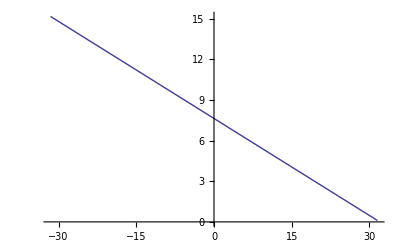

```mathematica
Plot[τ[Vs,ω],{ω,-noloadspeed,noloadspeed}]
```

```mathematica
τ[Vs,28]
```

0.954327

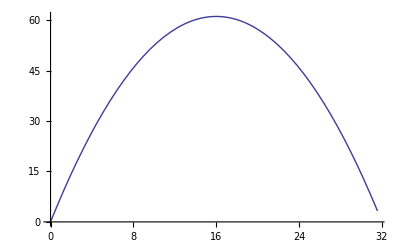

```mathematica
Plot[ ω*τ[Vs,ω],{ω,0,noloadspeed}]
```

```mathematica
16./(2π)
```

2.54648

```mathematica
1/2.55
```

0.392157

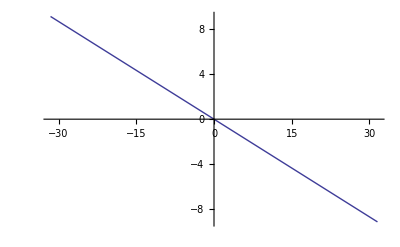

```mathematica
Plot[τ[0,ω],{ω,-noloadspeed,noloadspeed}]
```

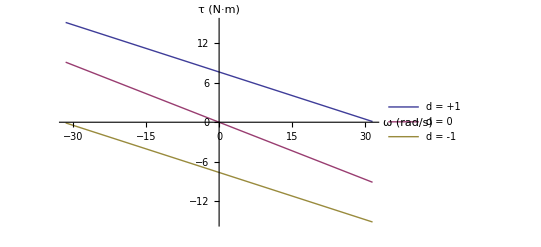

```mathematica
Plot[{τ[+Vs,ω],τ[0,ω],τ[-Vs,ω]},{ω,-noloadspeed,noloadspeed},PlotLegends->LineLegend[{"d = +1","d = 0","d = -1"}],AxesLabel->{"ω (rad/s)","τ (N·m)"}]
```